## First some definitions

```mathematica
CollatzLine[start_]:=Block[{current=start,next, result={}},
While[current≠1,
next=If[Mod[current,2]==0,current/2,(current*3+1)/2];
AppendTo[result,next ->current];
current=next;
];
result
]
```

```mathematica
CollatzForest[max_]:=CollatzForest[max]=Block[
{
 result,current, toAdd, size=Log[2,max]
},
result=Graph[{1},{1->2}];
If[IntegerQ[size],
];
If[
Monitor[
For[current=1,current≤max,current++,
If[!VertexQ[result,current],
toAdd=CollatzLine[current];
Table[If[!EdgeQ[result,edge],result=EdgeAdd[result,edge]],{edge,toAdd}];
]
],
ProgressIndicator[current,{1,max}]
];
result
]
```

```mathematica
CollatzLine[27]
```

{27→41,41→62,62→31,31→47,47→71,71→107,107→161,161→242,242→121,121→182,182→91,91→137,137→206,206→103,103→155,155→233,233→350,350→175,175→263,263→395,395→593,593→890,890→445,445→668,668→334,334→167,167→251,251→377,377→566,566→283,283→425,425→638,638→319,319→479,479→719,719→1079,1079→1619,1619→2429,2429→3644,3644→1822,1822→911,911→1367,1367→2051,2051→3077,3077→4616,4616→2308,2308→1154,1154→577,577→866,866→433,433→650,650→325,325→488,488→244,244→122,122→61,61→92,92→46,46→23,23→35,35→53,53→80,80→40,40→20,20→10,10→5,5→8,8→4,4→2,2→1}

```mathematica
CountConnected[x_,a_,aMax_]:=CountConnected[x,a]=Block[{g=CollatzForest[2^aMax], out, pow=2^a},
out=VertexOutComponent[g,x];
Select[out,#≤pow&]//Length
]
```

## Now some calcs

```mathematica
Table[CountConnected[k,10],{k,1,100}]
```

{1024,1023,9,1022,954,8,165,1021,7,944,419,7,469,164,7,66,449,6,172,943,6,253,434,6,30,468,6,156,237,6,81,65,5,29,454,5,137,171,5,473,46,5,55,252,5,426,166,5,107,29,5,18,464,5,39,155,5,64,59,5,399,80,5,58,100,4,75,28,4,19,175,4,28,136,4,140,57,4,11,472,4,39,57,4,27,54,4,14,69,4,262,425,4,84,48,4,16,106,4,23}

```mathematica
Table[Table[CountConnected[k,pow],{k,1,100}],{pow,2,15}]//MatrixForm
```

$Aborted

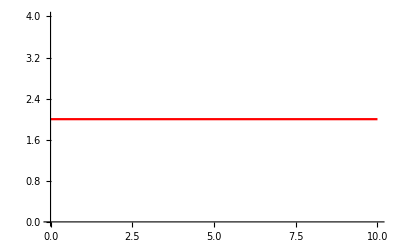

```mathematica
Plot[2,{x,0,10}, PlotStyle->Red]
```

Divide::infy: Infinite expression 1/0 encountered.

Divide::indet: Indeterminate expression 0/0 encountered.

Divide::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Divide::indet: Indeterminate expression 0/0 encountered.

General::stop: Further output of Divide::indet will be suppressed during this calculation.

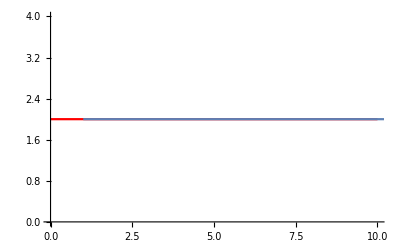
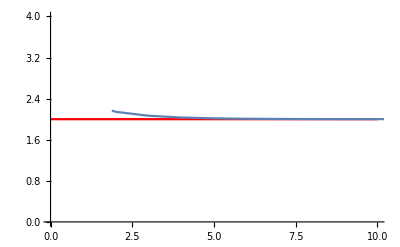
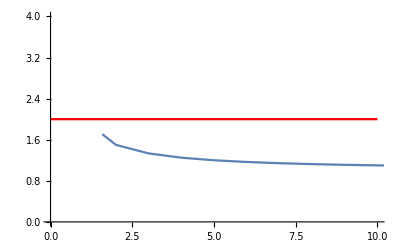
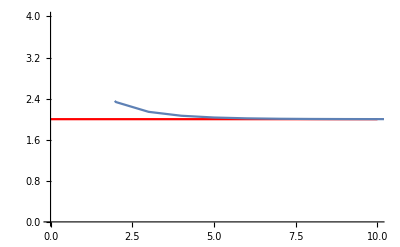
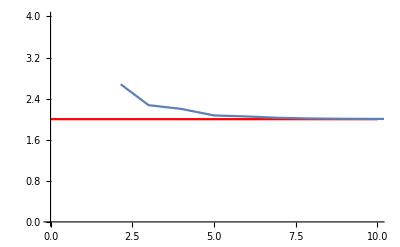
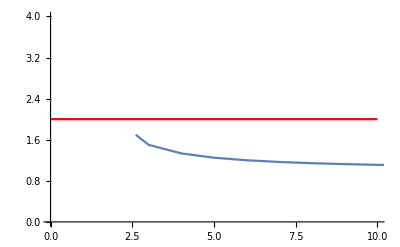
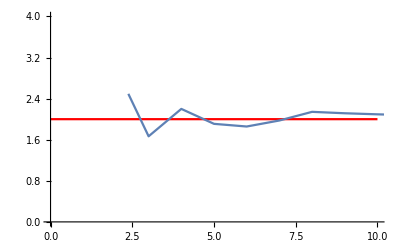
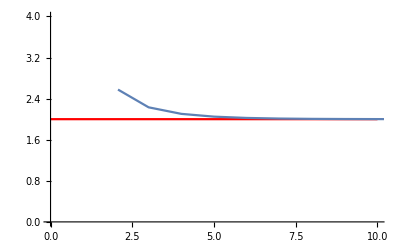
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[Plot[2,{x,0,10}, PlotStyle->Red],ListLinePlot[Table[CountConnected[k,pow,16],{pow,2,16}]//Ratios]],{k,1,100}]//N
```

```mathematica
CountConnected[40,11]
```

963

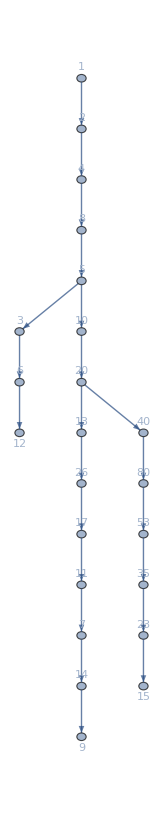

```mathematica
Graph[CollatzForest[30], VertexLabels->"Name", GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
{{□}, {□}}
```

```mathematica
Monitor[Table[Put[CollatzForest[2^k],"c:\\Saved\\collatz"<>ToString[k]<>".m"],{k,5,17}],k]
```

$Aborted